# Motion of a planet around a fixed center : compressions of angular data.

# 1 Newton’s compression.

## Newton’s equations (here in hamiltonian form) - together with the initial conditions set - accurately compress the data of measured angles θ (I1, I2 and I3 are the three autonomous invariants) :

## Initial conditions :

```mathematica
r0=16/10;th0=0;rprime0=0;thprime0=3/10;mu=1;
```

## Autonomous invariants :

```mathematica
I1=thprime0 r0^2;I2=I1 (rprime0 Sin[th0]+I1 Cos[th0]/r0)-mu Cos[th0];
I3=I1 (-rprime0 Cos[th0]+I1 Sin[th0]/r0)-mu Sin[th0];
```

```mathematica
{I1,I2,I3}
```

{96/125,-1973/3125,0}

## Period of the motion :

```mathematica
T=(2π mu I1^3)/((mu^2-I2^2-I3^2)^(3/2))
```

(250000 π)/(2549 √2549)

```mathematica
N[T]
```

6.10288

## Trajectory :

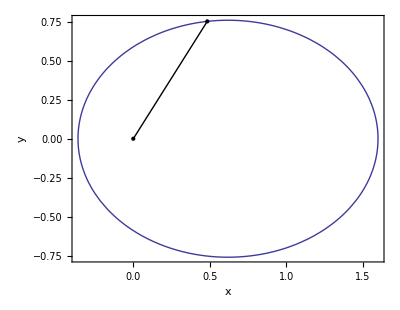

```mathematica
traj=PolarPlot[I1^2/(mu+I3 Sin[th]+I2 Cos[th]),{th,0,2Pi},Frame->True,PlotStyle->Thick,Epilog->{PointSize[Large],Point[{0,0}],Point[{u,v}={(I1^2 Cos[th])/(mu+I3 Sin[th]+I2 Cos[th]),(I1^2 Sin[th])/(mu+I3 Sin[th]+I2 Cos[th])}/.th->1],Thick,Line[{{0,0},{u,v}}]},LabelStyle->{Bold,Directive[14]},FrameLabel->{x,y}]
```

```mathematica
sol=NDSolve[{r'[t]==p[t],θ'[t]==q[t]/r[t]^2,p'[t]==q[t]^2/r[t]^3-mu/r[t]^2,q'[t]==0,r[0]==16/10,θ[0]==0,p[0]==0,q[0]==768/1000},{r,θ,p,q},{t,0,10.},WorkingPrecision->20]
```

{{r→InterpolatingFunction[{{0,10.}},<>],θ→InterpolatingFunction[{{0,10.}},<>],p→InterpolatingFunction[{{0,10.}},<>],q→InterpolatingFunction[{{0,10.}},<>]}}

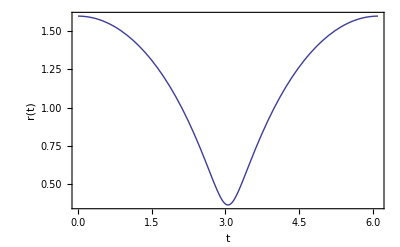

```mathematica
Plot[r[t]/.sol,{t,0,T},PlotStyle->Thick,Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,r[t]},LabelStyle->Large]
```

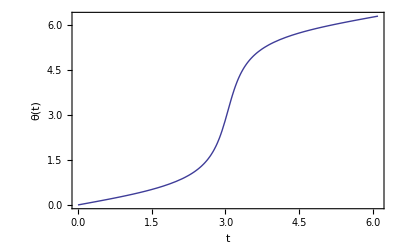

```mathematica
newton=Plot[θ[t]/.sol,{t,0,T},PlotStyle->Thick,Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,θ[t]},LabelStyle->Large]
```

## Distance between center and focus :

```mathematica
d=(-I2/mu)/(1-(I2/mu)^2)I1^2/mu
```

7892/12745

# 2 Hipparchus-like compression :

## A pure kinematical compression of θ as a function of t is possible on the ground of the Fourier-like false position, {x(t), y(t)} = {d+a1 Cos[(2π t)/T]+a2 Cos[(4π t)/T]+ ... ,b1 Sin[(2π t)/T]+b2 Sin[(4π t)/T]+ ... } :

```mathematica
data=Flatten[Table[{t,θ[t]}/.sol,{t,0,T/4,T/256}],1];
```

First approximation : one harmonic with period T (a1 and b1) :

```mathematica
NSolve[{Tan[θ[2]/.sol]==(b1 Sin[(2π 2)/T])/(d+a1 Cos[(2π 2)/T]),Tan[θ[4]/.sol]==(b1 Sin[(2π 4)/T])/(d+a1 Cos[(2π 4)/T])},{a1,b1}]
```

{{a1→0.655881823299764669,b1→0.352826029839046795}}

## A very off-centered elliptic trajectory :

```mathematica
{a1=0.655881823,b1=0.352826029};
```

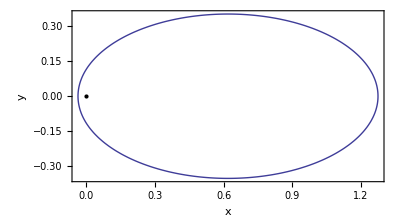

```mathematica
g1=ParametricPlot[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}/.{a1->0.65588182329976466864225477964279388073`18.,b1->0.35282602983904679545352260487682507115`18.},{t,0,T},PlotStyle->Thick,Frame->True,Epilog->{PointSize[Large],Point[{0,0}]},PlotStyle->Thick,Frame->True,LabelStyle->{Bold,Directive[14]},LabelStyle->Large,FrameLabel->{x,y}]
```

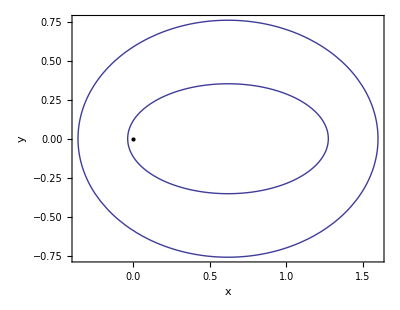

```mathematica
Show[PolarPlot[I1^2/(mu+I3 Sin[th]+I2 Cos[th]),{th,0,2Pi},Frame->True,Epilog->{PointSize[Large],Point[{0,0}]},PlotStyle->Thick,LabelStyle->{Bold,Directive[14]},FrameLabel->{x,y}],g1]
```

## A geometrical construction involving two generating circles :

```mathematica
Animate[Show[g1,Graphics[{PointSize[Large],Point[{0,0}],Red,Point[{d,0}],{Dashed,Circle[{d,0},(a1+b1)/2]},Dashed,Line[{{d,0},{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}}],Darker[Green],Point[{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}],{Dashed,Circle[{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]},(a1-b1)/2]},Line[{{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]},{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}+(a1-b1)/2{Cos[(2π t)/T],Sin[-(2π t)/T]}}],Black,Point[{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}+(a1-b1)/2{Cos[(2π t)/T],Sin[-(2π t)/T]}]}],PlotRange->All],{t,0,T},AnimationRepetitions->1,AnimationRunning->True,AnimationRate->0.1]
```

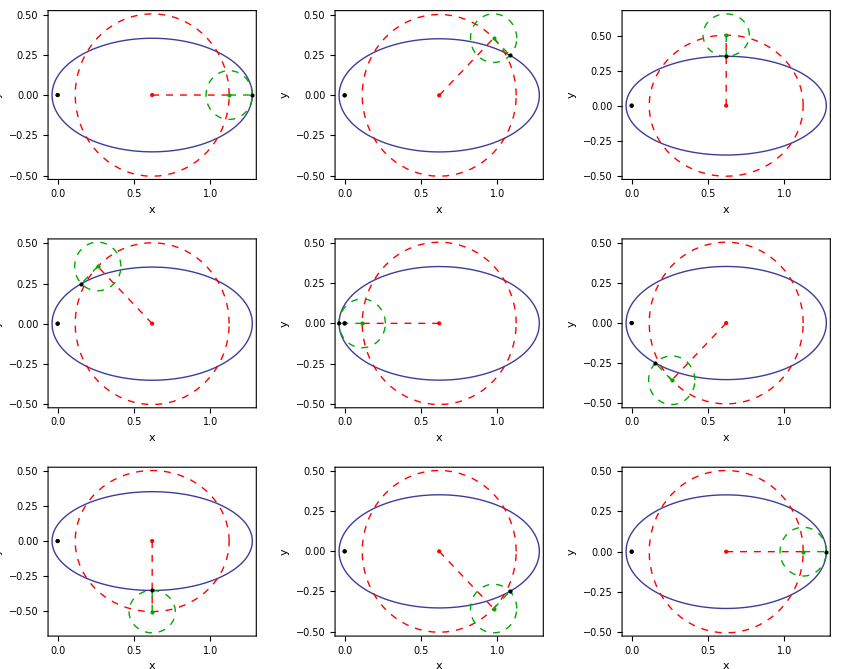

```mathematica
GraphicsGrid[Partition[Table[Show[g1,Graphics[{PointSize[Large],Point[{0,0}],Red,Point[{d,0}],{Dashed,Circle[{d,0},(a1+b1)/2]},Dashed,Line[{{d,0},{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}}],Darker[Green],Point[{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}],{Dashed,Circle[{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]},(a1-b1)/2]},Line[{{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]},{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}+(a1-b1)/2{Cos[(2π t)/T],Sin[-(2π t)/T]}}],Black,Point[{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}+(a1-b1)/2{Cos[(2π t)/T],Sin[-(2π t)/T]}]}],PlotRange->All],{t,0,T,T/8}],3]]
```

## How well θ(t) is approximated (Newton in black and Hipparchus in red) :

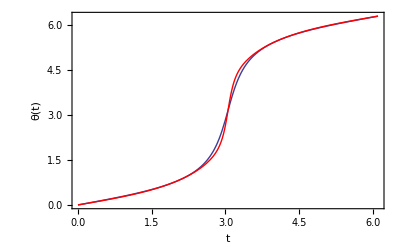

```mathematica
Show[newton,Plot[ ArcTan[d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]],{t,0,T/2},PlotStyle->Red,PlotStyle->Thick,Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,θ[t]},LabelStyle->Large],Plot[ 2Pi+ArcTan[d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]],{t,T/2,T},PlotStyle->Red,PlotStyle->Thick,Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,θ[t]},LabelStyle->Large]]
```

## Absolute error :

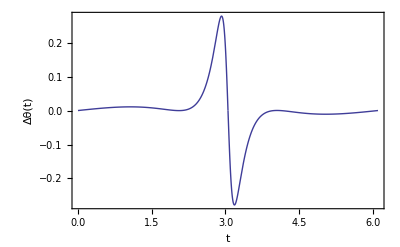

```mathematica
Show[Plot[(θ[t]/.sol)- ArcTan[d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]],{t,0,T/2},PlotStyle->Thick,PlotRange->All,Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,Δθ[t]},LabelStyle->Large],Plot[(θ[t]/.sol)- 2Pi-ArcTan[d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]],{t,T/2,T},PlotStyle->Thick,PlotRange->All,Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,Δθ[t]},LabelStyle->Large]]
```

Second approximation : two harmonics with periods T and T/2 (a1, a2, b1 and b2) :

```mathematica
Clear[a1,b1]
```

```mathematica
NSolve[{Tan[θ[2]/.sol]==(b1 Sin[(2π 2)/T]+b2 Sin[(2π 4)/T])/(d+a1 Cos[(2π 2)/T]+a2 Cos[(2π 4)/T]),Tan[θ[2.5]/.sol]==(b1 Sin[(2π 2.5)/T]+b2 Sin[(2π 5)/T])/(d+a1 Cos[(2π 2.5)/T]+a2 Cos[(2π 5)/T]),Tan[θ[3.5]/.sol]==(b1 Sin[(2π 3.5)/T]+b2 Sin[(2π 7)/T])/(d+a1 Cos[(2π 3.5)/T]+a2 Cos[(2π 7)/T]),Tan[θ[4]/.sol]==(b1 Sin[(2π 4)/T]+b2 Sin[(2π 8)/T])/(d+a1 Cos[(2π 4)/T]+a2 Cos[(2π 8)/T])},{a1,a2,b1,b2}]
```

{{a1→0.788279,a2→0.153621,b1→0.269198,b2→0.0896554}}

## This time, θ(t) is well approximated (Newton in black and Hipparchus in red) :

```mathematica
{a1=0.78827896,a2=0.15362132,b1=0.26919801,b2=0.08965540};
```

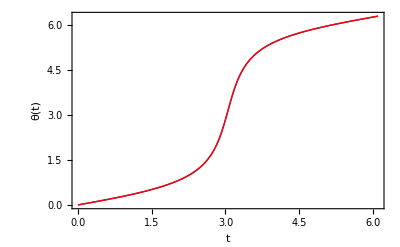

```mathematica
Show[newton,Plot[ ArcTan[d+a1 Cos[(2π t)/T]+a2 Cos[(4π t)/T],b1 Sin[(2π t)/T]+b2 Sin[(4π t)/T]],{t,0,T/2},PlotStyle->Red,PlotStyle->Thick,Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,θ[t]},LabelStyle->Large],Plot[ 2Pi+ArcTan[d+a1 Cos[(2π t)/T]+a2 Cos[(4π t)/T],b1 Sin[(2π t)/T]+b2 Sin[(4π t)/T]],{t,T/2,T},PlotStyle->Red,PlotStyle->Thick,Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,θ[t]},LabelStyle->Large]]
```

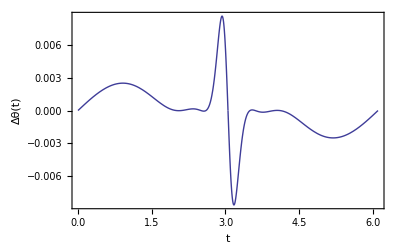

```mathematica
Show[Plot[(θ[t]/.sol)-ArcTan[d+a1 Cos[(2π t)/T]+a2 Cos[(4π t)/T],b1 Sin[(2π t)/T]+b2 Sin[(4π t)/T]],{t,0,T/2},PlotStyle->Thick,PlotRange->All,Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,Δθ[t]},LabelStyle->Large],Plot[(θ[t]/.sol)- 2Pi-ArcTan[d+a1 Cos[(2π t)/T]+a2 Cos[(4π t)/T],b1 Sin[(2π t)/T]+b2 Sin[(4π t)/T]],{t,T/2,T},PlotStyle->Thick,PlotRange->All,Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,Δθ[t]},LabelStyle->Large]]
```

## The trajectory is no more an ellipse (!) :

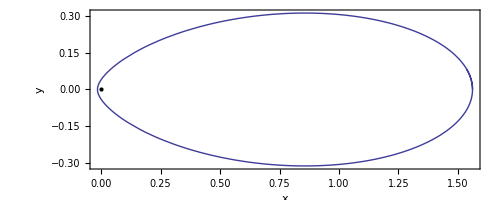

```mathematica
g2=ParametricPlot[{d+a1 Cos[(2π t)/T]+a2 Cos[(4π t)/T],b1 Sin[(2π t)/T]+b2 Sin[(4π t)/T]},{t,0,2Pi},Epilog->{PointSize[Large],Point[{0,0}]},PlotStyle->Thick,PlotRange->All,Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{x,y},LabelStyle->Large]
```

## A geometrical construction involving four generating circles :

```mathematica
Animate[Show[g2,Graphics[{PointSize[Large],Thick,Point[{0,0}],Red,Point[{d,0}],{Dashed,Circle[{d,0},(a1+b1)/2]},Darker[Green],Point[{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}],Dashed,Red,Line[{{d,0},{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}}],{Dashed,Darker[Green],Circle[{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]},(a1-b1)/2]},Green,Point[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}],Line[{{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]},{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}}],Darker[Magenta],{Dashed,Circle[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]},(a2+b2)/2]},Point[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}],

Darker[Magenta],Point[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}],

Line[{{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]},{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{(a2+b2)/2 Cos[2(2π t)/T],(a2+b2)/2 Sin[2(2π t)/T]}}],

{Dashed,Circle[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]},(a2+b2)/2]},Black,
{Dashed,Circle[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{(a2+b2)/2 Cos[2(2π t)/T],(a2+b2)/2 Sin[2(2π t)/T]},(a2-b2)/2]},

Point[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{(a2+b2)/2 Cos[2(2π t)/T],(a2+b2)/2 Sin[2(2π t)/T]}],


Black,Line[{{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{(a2+b2)/2 Cos[2(2π t)/T],(a2+b2)/2 Sin[2(2π t)/T]},{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{a2 Cos[2(2π t)/T],b2  Sin[2(2π t)/T]}}],Point[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{a2 Cos[2(2π t)/T],b2  Sin[2(2π t)/T]}]  } ],PlotRange->All],{t,0,T},AnimationRepetitions->1,AnimationRunning->True,AnimationRate->0.1]
```

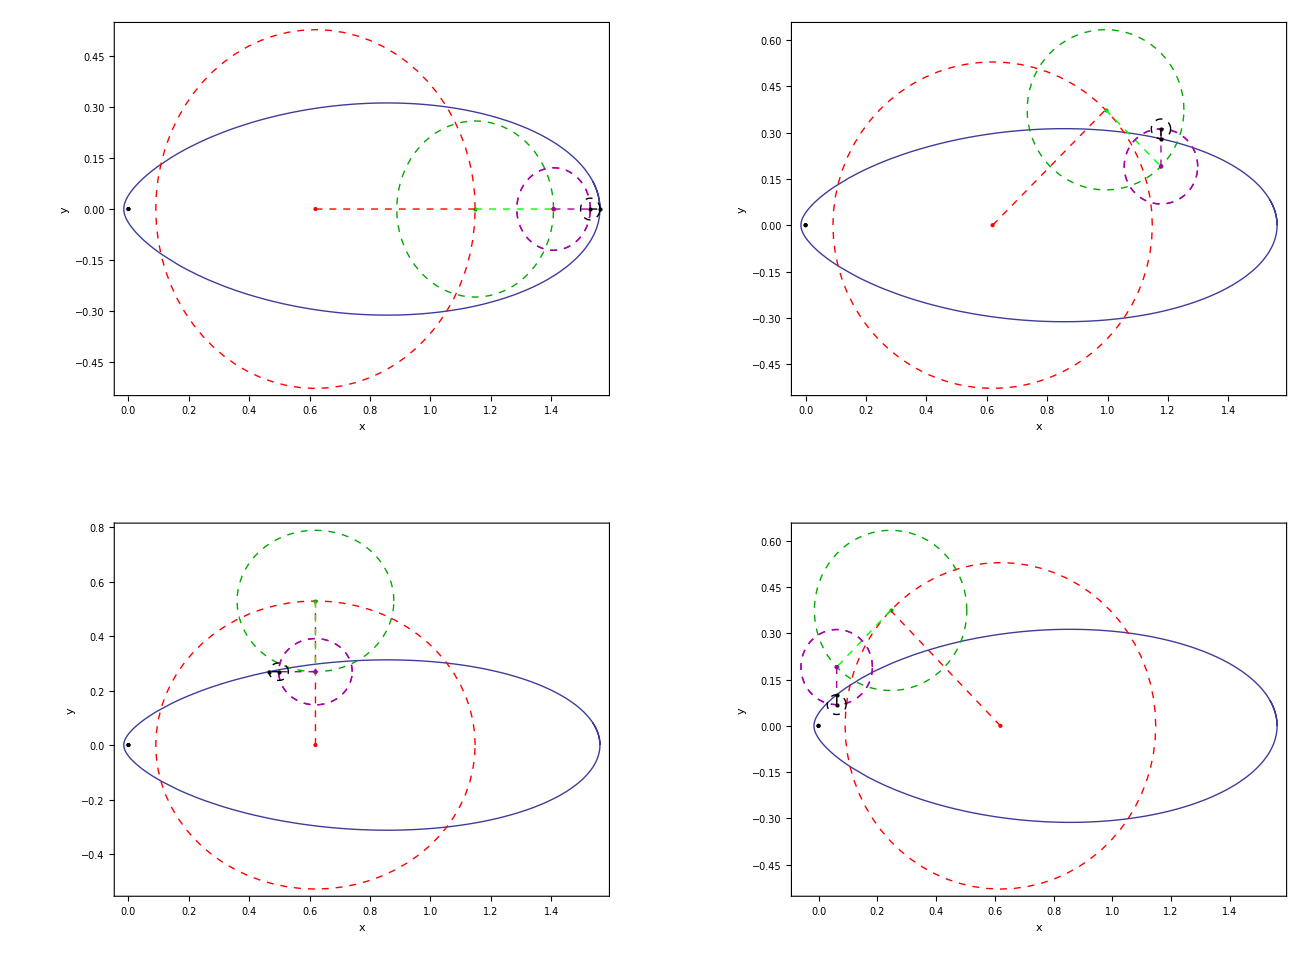

```mathematica
GraphicsGrid[Partition[Table[Show[g2,Graphics[{PointSize[Large],Thick,Point[{0,0}],Red,Point[{d,0}],{Dashed,Circle[{d,0},(a1+b1)/2]},Darker[Green],Point[{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}],Dashed,Red,Line[{{d,0},{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]}}],{Dashed,Darker[Green],Circle[{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]},(a1-b1)/2]},Green,Point[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}],Line[{{d+(a1+b1)/2 Cos[(2π t)/T],(a1+b1)/2 Sin[(2π t)/T]},{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}}],Darker[Magenta],{Dashed,Circle[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]},(a2+b2)/2]},Point[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}],

Darker[Magenta],Point[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}],

Line[{{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]},{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{(a2+b2)/2 Cos[2(2π t)/T],(a2+b2)/2 Sin[2(2π t)/T]}}],

{Dashed,Circle[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]},(a2+b2)/2]},Black,
{Dashed,Circle[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{(a2+b2)/2 Cos[2(2π t)/T],(a2+b2)/2 Sin[2(2π t)/T]},(a2-b2)/2]},

Point[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{(a2+b2)/2 Cos[2(2π t)/T],(a2+b2)/2 Sin[2(2π t)/T]}],


Black,Line[{{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{(a2+b2)/2 Cos[2(2π t)/T],(a2+b2)/2 Sin[2(2π t)/T]},{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{a2 Cos[2(2π t)/T],b2  Sin[2(2π t)/T]}}],Point[{d+a1 Cos[(2π t)/T],b1 Sin[(2π t)/T]}+{a2 Cos[2(2π t)/T],b2  Sin[2(2π t)/T]}]  } ],PlotRange->All],{t,0,T/2,T/8}],2]]
```